## Reddit subreddit analyzer

Sai kumar Murali krishnan
John Monash Science School

## Description

#### Goal:

Produce a webapp that scrapes a subreddit when given input. This data will be intepreted in various forms including:

Popular words in a subreddit
- Upvoted posts
Time analysis e.g time posted and upvote correlation
Union of common words and popular words

This will retrieve data using Reddit’s API and analyze text such as posts or comments. This will then be visualized for further understanding.

## Webpage (NOT IN USE, IGNORE)

```mathematica
CloudDeploy[FormFunction[{
"x"-> <|"Label"-> "Choose a subreddit",
"Interpreter"->"String"|>

},

(
Grid[{
{Block[{d=Table[reddit["SubredditPosts","Subreddit"-> #x,"ShowThumbnails"->True][[2]][[x]][[6]],{x,2}]},

f=Dataset[reddit["PostCommentsData","Post"-> ToString[#],MaxItems->200]["Post"]]["Selftext"]&/@d]},
{"hi"},
{"lol"},
{Hyperlink["Start over?","https://lab.wolframcloud.com/objects/mur0013/redditDataProject"]}
}])&
,

AppearanceRules-><|"Title"-> "Subreddit Analyser",
"Description"-> "Returns statistics about a subreddit.",
"SubmitLabel"->"Retrieve info",
"ItemLayout"->"Vertical"|>
]

,"redditDataProject","Permissions"->"Public" ]
```

CloudObject[https://www.wolframcloud.com/objects/mur0013/redditDataProject]

https://lab.wolframcloud.com/objects/mur0013/redditDataProject

The webpage will not be useable until the API can be successfully implemented into the cloud.

## Functions

```mathematica
reddit=ServiceConnect["Reddit"]
```

ServiceObject[…]

```mathematica
WordICloud[bodyList_]:=
Block[
{a=DeleteStopwords@Flatten[TextWords/@Normal[bodyList]]},
WordCloud[Pick[a,Classify["Profanity",a],False]]]
```

```mathematica
GetComments[post_,limit_]:=
Block[{s=Dataset[reddit["PostCommentsData","Post"->ToString[post],MaxItems->500]]["Comments"],
l=Length[Dataset[reddit["PostCommentsData","Post"->ToString[post],MaxItems->500]]["Comments"]]},

Table[s⟦x⟧["Body"],{x,1,Ceiling[l/limit]}]]
```

```mathematica
GetUpvotes[post_]:=
Block[{s=Dataset[reddit["PostCommentsData","Post"->ToString[post],MaxItems->500]]["Comments"],
l=Length[Dataset[reddit["PostCommentsData","Post"->ToString[post],MaxItems->500]]["Comments"]]},

Table[s⟦x⟧["Score"],{x,1,l}]]
```

```mathematica
GetBatchURLS[subreddit_,number_,sort_]:=
Block[
{info=reddit["SubredditPosts","Subreddit"-> ToString[subreddit],"ShowThumbnails"->True,"SortBy"->sort]⟦2⟧},
Flatten[f=Table[info⟦x⟧⟦8⟧,{x,number}]]]
```

```mathematica
GetBatchPosts[subreddit_,number_,sort_]:=
Block[{info=reddit["SubredditPosts","Subreddit"-> ToString[subreddit],"SortBy"->sort]⟦2⟧},
Block[{d=Table[info⟦x⟧⟦8⟧,{x,number}]},
{
If[Dataset[reddit["PostCommentsData","Post"-> ToString[#],MaxItems->200,"ShowThumbnails"->True]]["Post"]["Over18"],

"NSFW",

{Dataset[reddit["PostCommentsData","Post"-> ToString[#],MaxItems->200,"ShowThumbnails"->True]]["Post"]["Title"],

Dataset[reddit["PostCommentsData","Post"-> ToString[#],MaxItems->200,"ShowThumbnails"->True]["Post"]]["Thumbnail"],

Dataset[reddit["PostCommentsData","Post"-> ToString[#],MaxItems->200]]["Post"]["Selftext"]}]

&/@d}]]
```

```mathematica
GetPosts[post_]:=
{reddit["PostCommentsData","Post"->post,MaxItems->200]["Post"]["Title"],
reddit["PostCommentsData","Post"->post,MaxItems->200]["Post"]["Selftext"],
reddit["PostCommentsData","Post"-> post,MaxItems->200,"ShowThumbnails"->True]["Post"]["Thumbnail"]}
```

```mathematica
CommentGraph[comments_]:=
Block[{simi=Flatten[Outer[Rule,{#},Nearest[DeleteCases[Normal[comments],#],#]]&/@Normal[comments]]},

Block[{g=Graph[simi,VertexSize->Normal[comments
],VertexLabels->Placed["Name",Tooltip],DirectedEdges->False,ImageSize->Large]},

CommunityGraphPlot[#,FindGraphCommunities[#],CommunityRegionStyle->Directive[Opacity[.05],Gray],CommunityBoundaryStyle->Directive[Red,Dotted],Method->"SpringElectrical",ImageSize->Large]&@g]]
```

```mathematica
BatchCommentGraph[subreddit_,limit_,posts_,sort_]:=
Block[{urls=GetBatchURLS[ToString[subreddit],posts,sort]},

Block[{commblock=Flatten[(GetComments[#,limit]&/@urls)]},

CommentGraph[Flatten[commblock]]]]
```

```mathematica
BatchPostingStatistics[posts_]:=
Block[{tab=Table[reddit["PostCommentsData","Post"->ToString[posts[[x]]],MaxItems->500,"Depth"->4]["Comments"],{x,1,Length[posts]}]},

Block[{f=Flatten[Table[Table[tab⟦y⟧⟦x⟧["CreationDate"],{x,1,Length[tab⟦y⟧]}],    {y,1,Length[tab]}]]},

ImageCollage[DateHistogram[f,#,Axes->False,Frame->True,FrameLabel->{Automatic,#},ImageSize->Large,BaseStyle->Directive[20,Black]]&/@{"Hour","Day","Week","Month","Year"},Background->White]]]
```

```mathematica
PostingStatistics[post_]:=
Block[{tab=reddit["PostCommentsData","Post"->ToString[post],MaxItems->500,"Depth"->4]["Comments"]},

Block[{f=Table[tab[[x]]["CreationDate"],{x,1,Length[tab]}]},

ImageCollage[DateHistogram[f,#,Axes->False,Frame->True,FrameLabel->{Automatic,#},ImageSize->Large,BaseStyle->Directive[20,Black]]&/@{"Minute","Hour","Day","Week","Month","Year"},Background->White]]]
```

```mathematica
HotWords[posts_]:=
WordCloud[DeleteStopwords[Flatten[TextWords[Flatten[(GetComments[#,1]&/@posts)][[;;15]]]]]]
```

## Code:

### Subreddits used: r/math r/science r/gaming r/worldnews

#### We can retrieve the comments of a single post with GetComments and specify a limit to cut down large posts:

```mathematica
GetComments["https://www.reddit.com/r/math/comments/8aardr/simple_questions/",1][[1]]
```

Can you write 3D or higher dimensional spheres in terms of sin and cos?

How?

The parameters for GetComments are as follows:
GetComments[posturl, comment limiter]

#### To retrieve the body, title and thumbnail of a single post, use GetPosts:

```mathematica
GetPosts["https://www.reddit.com/r/science/comments/8bs8b1/a_new_study_suggests_that_the_overrepresentation/"]
```

{A new study suggests that the overrepresentation of wild animals in our everyday lives (toys, films, ads) makes us forget that they are on the verge of extinction. Researchers believe companies should pay 'image rights' to help conservation efforts,,-Graphics-}

The only parameter for GetPosts is the post.

#### Instead of retrieving a specific post, you can retrieve a batch of posts:

```mathematica
GetBatchPosts["math",2,"Top"]
```

{{{Zeta function painting from my super special girlfriend, I think you will like it!,-Graphics-,},{Today I learned that every palindromic number with an even number of digits is a multiple of 11.,Missing[NotAvailable],Every number (in decimal) that is a palindrome and has an even number of digits is divisible by 11.

The condition is not true the other way around however; a number times 11 will not nessecarily be an even-digit palindrome.  But *every* palindrome with an even number of digits is a multiple of 11. }}}

Sometimes a post will return Missing[NotAvailable]. This signifies the post in question has no body or has no thumbnail.
The parameters for GetBatchPosts are:
GetBatchPosts[subreddit, number of posts, SortBy]
SortBy can be: “New”, “Top”, “Hot”, or “Controversial”

#### To scrape the urls of the posts from a subreddit:

```mathematica
GetBatchURLS["showerthoughts",5,"Hot"]
```

{http://www.reddit.com/r/Showerthoughts/comments/7xde4g/what_is_a_showerthought/,http://www.reddit.com/r/Showerthoughts/comments/8brak2/there_are_two_types_of_hotel_guests_in_the_world/,http://www.reddit.com/r/Showerthoughts/comments/8bp7bc/future_kids_will_be_flabbergasted_that_we_used_to/,http://www.reddit.com/r/Showerthoughts/comments/8bosam/since_your_internal_voice_doesnt_have_to_breath/,http://www.reddit.com/r/Showerthoughts/comments/8bqk5j/we_ask_complete_strangers_to_watch_our_stuff_when/}

The parameters are the same as GetBatchPosts.

#### Now, to make a graph of losely related comments in a post:

```mathematica
comments=GetComments["https://www.reddit.com/r/gaming/comments/8brdrs/my_teammates_in_a_nutshell/",1];
```

```mathematica
CommentGraph[comments]
```

-Graphics-

#### To create a comment graph for a batch of posts:

```mathematica
BatchCommentGraph["math",3,5,"Top"]
```

-Graphics-

The parameters for BatchCommentGraph are:
BatchCommentGraph[subreddit, limiter, number of posts, SortBy]

```mathematica
BatchCommentGraph["popular",3,6,"Hot"]
```

-Graphics-

#### Create a world cloud of comments in several posts:

```mathematica
post=GetBatchURLS["worldnews",5,"Hot"];
```

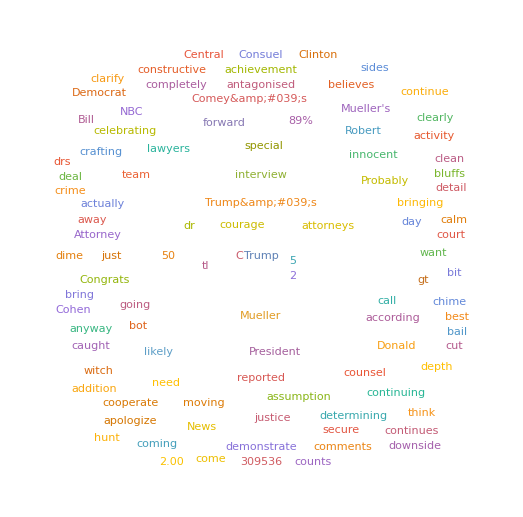

```mathematica
HotWords[post]
```

```mathematica
post2 = GetBatchURLS["starwars",5,"Hot"];
```

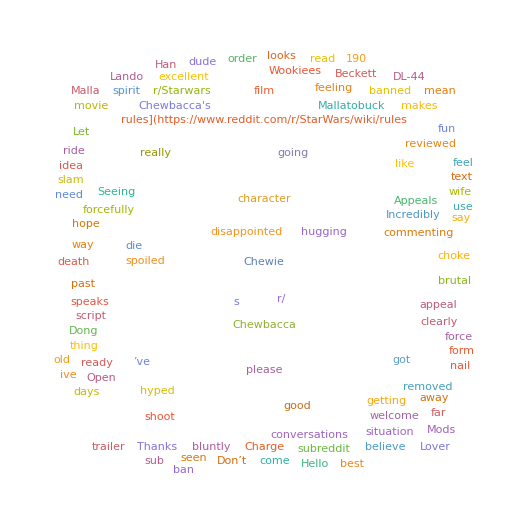

```mathematica
HotWords[post2]
```

#### Create a posting time histogram:

```mathematica
PostingStatistics["https://www.reddit.com/r/Showerthoughts/comments/8brak2/there_are_two_types_of_hotel_guests_in_the_world/"]
```

-Graphics-

#### To do so for multiple posts:

```mathematica
timeset=GetBatchURLS["todayilearned",5,"Hot"];
```

```mathematica
BatchPostingStatistics[timeset]
```

-Graphics-

## Archive:

```mathematica
GetBatchPosts["explainlikeimfive",5]
```

```mathematica
dat=reddit["PostCommentsData","Post"->"https://www.reddit.com/r/IAmA/comments/2j4ce1/keanu_reeves_he",MaxItems->200]["Comments"];
```

```mathematica
dat=GetComments["https://www.reddit.com/r/jailbreak/comments/8brzv1/discussion_gets_bashed_by_the_community_for/",5]
```

```mathematica
reddit["SubredditPosts","Subreddit"-> "askreddit","ShowThumbnails"->True,"SortBy"->"Top"]⟦2⟧;
```

```mathematica
CommentGraph[dat]
```

-Graphics-

```mathematica
a=GetBatchURLS["askreddit",10];
```

```mathematica
CommentGraph[dat]
```

Outer::heads: Heads Nearest and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair cl8ac0f and <|SubredditID→t5_2qzb6,approved_at_utc→Missing[NotAvailable],Ups→3906,mod_reason_by→Missing[NotAvailable],BannedBy→Missing[NotApplicable],author_flair_type→text,RemovalReason→Missing[NotApplicable],LinkID→t3_2j4ce1,Likes→Missing[NotAvailable],no_follow→False,Replies→{},UserReports→{},Saved→False,ID→cl8a4zd,banned_at_utc→Missing[NotAvailable],mod_reason_title→Missing[NotAvailable],Gilded→0,Archived→True,«17»,can_gild→True,Subreddit→IAmA,author_flair_text_color→Missing[NotAvailable],ScoreHidden→False,permalink→/r/IAmA/comments/2j4ce1/keanu_reeves_hello/cl8a4zd/,ReportsCount→Missing[NotAvailable],GlobalID→t1_cl8a4zd,AuthorFlairText→Missing[NotAvailable],rte_mode→markdown,CreationDate→Mon 13 Oct 2014 15:50:53,SubredditNamePrefix→r/IAmA,Controversiality→0,Depth→0,author_flair_background_color→Missing[NotAvailable],ModReports→{},mod_note→Missing[NotAvailable],Distinguished→Missing[NotAvailable],Kind→t1|>.

FindGraphCommunities::graph: A graph object is expected at position 1 in FindGraphCommunities[Graph[{«1»},VertexSize→{<|SubredditID→t5_2qzb6,approved_at_utc→Missing[NotAvailable],Ups→3906,mod_reason_by→Missing[NotAvailable],BannedBy→Missing[NotApplicable],author_flair_type→text,RemovalReason→Missing[NotApplicable],LinkID→t3_2j4ce1,Likes→Missing[NotAvailable],no_follow→False,Replies→{},UserReports→{},Saved→False,ID→cl8a4zd,banned_at_utc→Missing[NotAvailable],mod_reason_title→Missing[NotAvailable],«21»,author_flair_text_color→Missing[NotAvailable],ScoreHidden→False,permalink→/r/IAmA/comments/2j4ce1/keanu_reeves_hello/cl8a4zd/,ReportsCount→Missing[NotAvailable],GlobalID→t1_cl8a4zd,AuthorFlairText→Missing[NotAvailable],rte_mode→markdown,CreationDate→Mon 13 Oct 2014 15:50:53,SubredditNamePrefix→r/IAmA,Controversiality→0,Depth→0,author_flair_background_color→Missing[NotAvailable],ModReports→{},mod_note→Missing[NotAvailable],Distinguished→Missing[NotAvailable],Kind→t1|>,<|Su…tID→…,«52»|>,«48»,«133»},«1»,«1»,ImageSize→Large]].

CommunityGraphPlot::graph: A graph object is expected at position 1 in CommunityGraphPlot[Graph[{«1»},VertexSize→{«1»},VertexLabels→Placed[Name,Tooltip],DirectedEdges→False,ImageSize→Large],«4»,ImageSize→Large].

CommunityGraphPlot[1]
 |  |  |  |

```mathematica
CommunityGraphPlot[#,FindGraphCommunities[#],CommunityRegionStyle->Directive[Opacity[.05],Gray],CommunityBoundaryStyle->Directive[Red,Dotted],Method->"SpringElectrical",ImageSize->Large]&@g
```

```mathematica
g=Graph[similarities,VertexSize->Normal[t
],VertexLabels->Placed["Name",Tooltip],DirectedEdges->False,ImageSize->Large]
```

```mathematica
g=Graph[similarities,VertexSize->Normal[data[All,#["Body"]->{"Scaled",#["Score"]/150000}&]],VertexLabels->Placed["Name",Tooltip],DirectedEdges->False,ImageSize->Large]
```

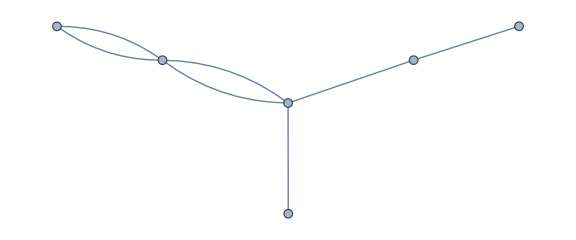

```mathematica
similarities=Flatten[Outer[Rule,{#},Nearest[DeleteCases[Normal[dat],#],#]]&/@Normal[dat]];

g=Graph[similarities,VertexSize->Normal[data[All,#["Body"]->{"Scaled",#["Score"]/1000}&]],VertexLabels->Placed["Name",Tooltip],DirectedEdges->False,ImageSize->Large]
```

```mathematica
BatchCommentGraph[subreddit_,limit_,posts_,sort_]
```

```mathematica
BatchCommentGraph["explainlikeimfive",5,4,"Top"]
```

-Graphics-

```mathematica
BatchCommentGraph["askreddit",4,10]
```

-Graphics-

```mathematica
BatchCommentGraph["fireemblemheroes",5,5]
```

-Graphics-

```mathematica
GetBatchURLS["kingdomhearts",10,"Top"]
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
GetBatchURLS["showerthoughts",10,"Top"]
```

{http://www.reddit.com/r/Showerthoughts/comments/7d1kop/if_ea_suffers_big_enough_losses_from_the_backlash/,http://www.reddit.com/r/Showerthoughts/comments/7mhv6a/anxiety_is_like_when_video_game_combat_music_is/,http://www.reddit.com/r/Showerthoughts/comments/7h9y6v/somebody_at_google_was_just_like_yea_just_have/,http://www.reddit.com/r/Showerthoughts/comments/7o6kn8/college_students_dont_want_to_go_to_graduation/,http://www.reddit.com/r/Showerthoughts/comments/7cif01/it_kinda_makes_sense_that_the_target_audience_for/,http://www.reddit.com/r/Showerthoughts/comments/7ox9b3/being_35_and_not_wanting_to_work_in_the_field_for/,http://www.reddit.com/r/Showerthoughts/comments/71xyoh/security_at_every_level_of_an_airport_is/,http://www.reddit.com/r/Showerthoughts/comments/7xngk6/the_olympics_is_the_only_time_when_you_hear_great/,http://www.reddit.com/r/Showerthoughts/comments/83oc53/this_spring_forward_thing_would_be_a_lot_more/,http://www.reddit.com/r/Showerthoughts/comments/612f0c/tinder_is_the_opposite_of_porn_site/}

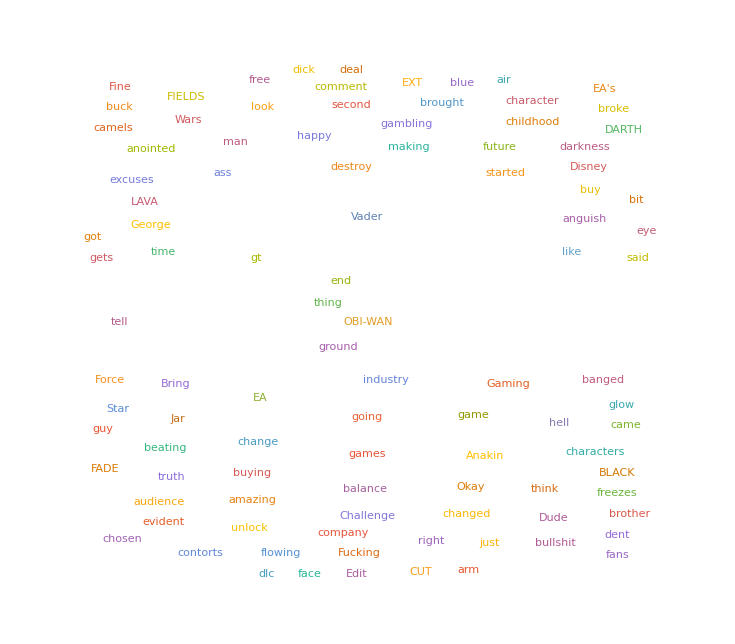

```mathematica
HotWords[%38]
```

```mathematica
tab=GetComments[%6[[2]],1]
```

```mathematica
f=Table[tab[[x]]["CreationDate"],{x,1,153}]
```

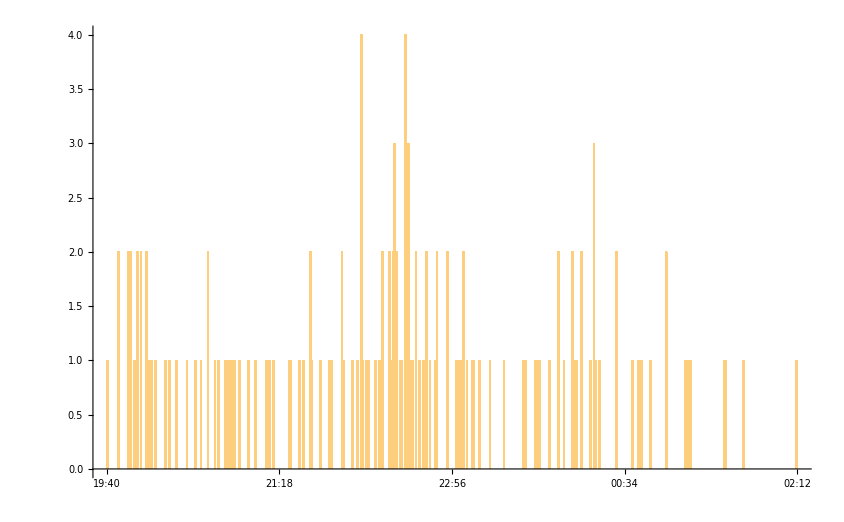

```mathematica
DateHistogram[f,"Minute"]
```

```mathematica
PostingStatistics["https://www.reddit.com/r/AskReddit/comments/8bjxwe/what_is_your_goto_neverfail_joke/"]
```

-Graphics-

```mathematica
GetBatchURLS["explainlikeimfive",5,"Top"]
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
BatchPostingStatistics[%24]
```

-Graphics-

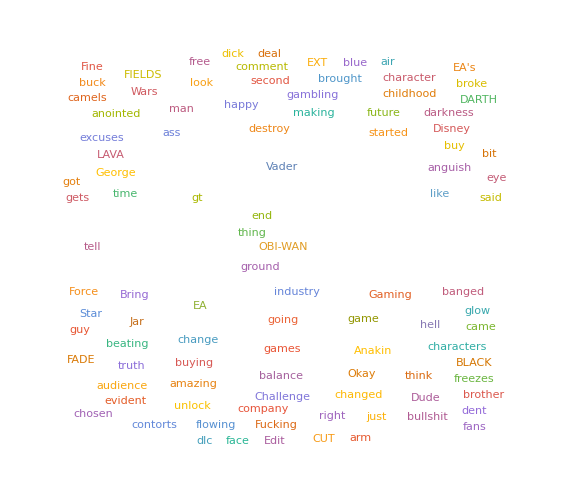

```mathematica
HotWords[%38]
```

```mathematica
BatchPostingStatistics[%6]
```

Part::partw: Part 11 of {Dataset[«191»],Dataset[«212»],Dataset[«15»],Dataset[«161»],Dataset[«23»],Dataset[«45»],Dataset[«14»],Dataset[«29»],Dataset[«29»],Dataset[«14»]} does not exist.

Part::partw: Part 12 of {Dataset[«191»],Dataset[«212»],Dataset[«15»],Dataset[«161»],Dataset[«23»],Dataset[«45»],Dataset[«14»],Dataset[«29»],Dataset[«29»],Dataset[«14»]} does not exist.

Part::partw: Part 13 of {Dataset[«191»],Dataset[«212»],Dataset[«15»],Dataset[«161»],Dataset[«23»],Dataset[«45»],Dataset[«14»],Dataset[«29»],Dataset[«29»],Dataset[«14»]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
tabe=Table[reddit["PostCommentsData","Post"->ToString[%9[[x]]],MaxItems->500]["Comments"],{x,1,Length[%9]}];
```

```mathematica
Length[%11]
```

10

```mathematica
tabe[[1]][[1]]["CreationDate"]
```

Sun 11 Jun 2017 05:45:38GMT

```mathematica
Flatten[Table[Table[tabe⟦y⟧⟦x⟧["CreationDate"],{x,1,Length[tabe⟦y⟧]}],    {y,1,Length[tabe]}]]
```

{Sun 11 Jun 2017 05:45:38GMT,Sun 11 Jun 2017 05:59:37GMT,Sun 11 Jun 2017 05:58:17GMT,Sun 11 Jun 2017 05:51:58GMT,Sun 11 Jun 2017 07:41:42GMT,Sun 11 Jun 2017 05:46:51GMT,Sun 11 Jun 2017 05:49:02GMT,Sun 11 Jun 2017 05:41:34GMT,Sun 11 Jun 2017 05:38:01GMT,Sun 11 Jun 2017 06:12:42GMT,Sun 11 Jun 2017 05:55:09GMT,Sun 11 Jun 2017 05:48:12GMT,Sun 11 Jun 2017 05:41:45GMT,Sun 11 Jun 2017 05:58:44GMT,Sun 11 Jun 2017 06:10:07GMT,Sun 11 Jun 2017 06:16:06GMT,807,Thu 15 Feb 2018 23:13:47GMT,Fri 16 Feb 2018 03:14:34GMT,Mon 30 Jan 2017 04:41:23GMT,Mon 30 Jan 2017 02:25:50GMT,Mon 30 Jan 2017 07:29:47GMT,Mon 30 Jan 2017 03:26:24GMT,Mon 30 Jan 2017 05:39:40GMT,Mon 30 Jan 2017 15:57:56GMT,Mon 30 Jan 2017 13:17:08GMT,Mon 30 Jan 2017 23:54:29GMT,Mon 30 Jan 2017 04:02:56GMT,Mon 30 Jan 2017 07:16:59GMT,Mon 30 Jan 2017 05:32:18GMT,Mon 30 Jan 2017 11:02:23GMT,Mon 30 Jan 2017 11:19:38GMT,Tue 31 Jan 2017 03:50:01GMT}
 |  |  |  |

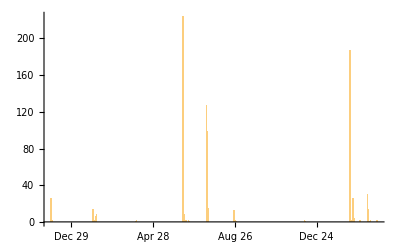

```mathematica
DateHistogram[%14,"Day"]
```

```mathematica
tabe[[9]][[1]]
```

Dataset[<>]

```mathematica
tab=reddit["PostCommentsData","Post"->"https://www.reddit.com/r/AskReddit/comments/8bjxwe/what_is_your_goto_neverfail_joke/",MaxItems->500,"Depth"->4]["Comments"]
```

Dataset[<>]

```mathematica
%99[[1]]
```

```mathematica
GetBatchURLS["worldnews",10,"Hot"]
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
GetComments[#,5]&/@%65
```

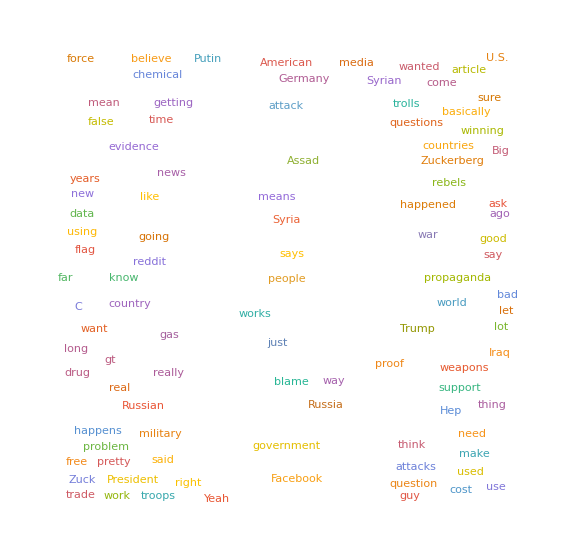

{1}
 |  |  |  |

```mathematica
WordICloud[Flatten[%68]]
```